# On Visualizing vector fields

## Assignment: 3

PH1050: Computational Physics

Aarya Gosar
EP23B025

Engineering Physics

6 Sept 2023

## Obtaining Vector Field at a point

```mathematica
(* coords = {ρ , θ,φ} *)
(* B = mu i dlxr/r^3 *)
```

```mathematica
Clear["Global`*"]
$Assumptions = { Im[ρ] == 0 && ρ > 0 && Re[L]≥0};
zCap = {0,0,1};
r= {ρ,0,z};
dB[z_] = Cross[zCap,r]/(Norm[r])^3;
B[L_] := Integrate[dB[z], {z,-L,L}]
B[L]
```

{0,(2 L)/(ρ √(L^2+ρ^2)),0}

```mathematica
BCartInfinite[x_,y_,z_] := TransformedField["Cylindrical" ->"Cartesian",Limit[ B[L] , L -> Infinity], {ρ,θ,φ}->{x,y,z}][[1;;2]]
BCartInfinite = BCartInfinite[x,y,z][[1;;2]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{-(2 y)/(x^2+y^2),(2 x)/(x^2+y^2)}

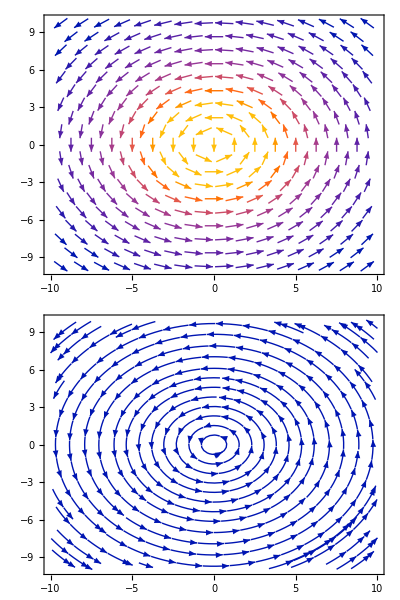

```mathematica
Column[{ VectorPlot[BCartInfinite, {x,-10,10}, {y,-10,10}],StreamPlot[BCartInfinite, {x,-10,10}, {y,-10,10}]}]
```

```mathematica
(* for a finite length*)
BCart[x_,y_,z_] := TransformedField["Cylindrical" ->"Cartesian", B[L], {ρ,θ,φ}->{x,y,z}][[1;;2]]
BCart = BCart[x,y,z][[1;;2]];
(* when L tends to infinity*)
Limit[BCart, L-> Infinity]
L = 1;
BCart
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{-(2 y)/(x^2+y^2),(2 x)/(x^2+y^2)}

{-(2 y)/((x^2+y^2) √(1+x^2+y^2)),(2 x)/((x^2+y^2) √(1+x^2+y^2))}

```mathematica
Print["For L = 1"]
Column[{ VectorDensityPlot[BCart, {x,-10,10}, {y,-10,10}],StreamPlot[BCart, {x,-10,10}, {y,-10,10}]}]
```

For L = 1

-Graphics-

## Tilted Dipole

```mathematica
Clear["Global`*"]
potentialSpherical = (p Cos[θ]+p Sin[θ] Sin[φ])/ρ^2/. p -> 1
fieldSpherical = -Grad[potentialSpherical, {ρ,θ,φ} , "Spherical"]

potentialCart[x_,y_,z_] := TransformedField["Spherical" ->"Cartesian", potentialSpherical, {ρ,θ,φ} ->{x,y,z}]/.p ->1
fieldCart[x_,y_,z_]:=TransformedField["Spherical"->"Cartesian",fieldSpherical,{ρ,θ,φ}->{x,y,z}]/. p->1
```

(Cos[θ]+Sin[θ] Sin[φ])/ρ^2

{(2 (Cos[θ]+Sin[θ] Sin[φ]))/ρ^3,-(-Sin[θ]+Cos[θ] Sin[φ])/ρ^3,-Cos[φ]/ρ^3}

```mathematica
fieldYZ[y_,z_]:=fieldCart[x,y,z]/. x->0
fieldYZ[y,z]//FullSimplify
potential = potentialCart[x,y,z]/.x->0
field=FullSimplify[fieldYZ[y,z][[2;;3]]]
```

{0,(2 y^2+3 y z-z^2)/((y^2+z^2)^(5/2)),(-y^2+3 y z+2 z^2)/((y^2+z^2)^(5/2))}

(y+z)/((y^2+z^2)^(3/2))

{(2 y^2+3 y z-z^2)/((y^2+z^2)^(5/2)),(-y^2+3 y z+2 z^2)/((y^2+z^2)^(5/2))}

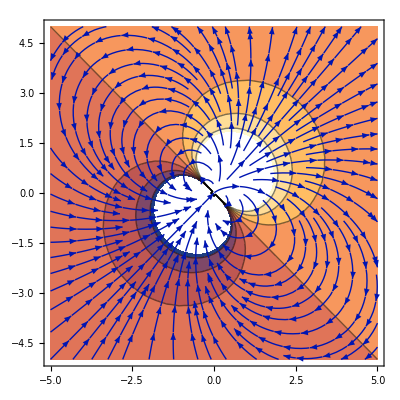

```mathematica
plt1 = StreamPlot[field, {y,-5,5} , {z,-5,5}];
plt2 = ContourPlot[potential,{y,-5,5} , {z,-5,5}];
Show[{plt2,plt1}]
```

## Distribution of charges

```mathematica
Clear["Global`*"]
charges = {}
addCharge[q_,x_,y_] := AppendTo[charges, {q,{x,y}}]
addCharge[2,3,4];
addCharge[-5,-3,-5];
charges
```

{}

{{2,{3,4}},{-5,{-3,-5}}}

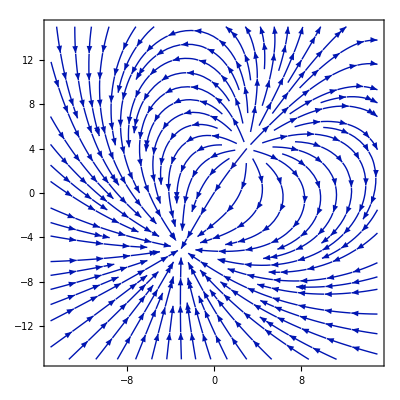

```mathematica
e = {0,0};
For[i=1,i<=Length[charges],i++, e = e + charges[[i]][[1]] * ({x,y} - charges[[i]][[2]])/Norm[({x,y} - charges[[i]][[2]])]^3]
StreamPlot[e,{x,-15,15} , {y,-15,15}]
```